# Conto Flow

Michael.Schreiber

Version 0.1

```mathematica
Print@DateString[]
```

Tue 5 Jun 2018 19:10:24

## Goals

1. Distinguish traditional transfer events from non traditional flows between contos. 
2. Simulate blockchains which support particular protocols for related features.
3. Find concise specifications which simplify verifications of implementations.

## Approach

Changes of conto balances are recorded with block time stamps according to rates of flows. 
Types of contos are defined upon creation to model players and supply is fixed by total initial balances.
Flows with arbitrary rates change particular effects of distribution but conserve total balances.
Accumulated results of flows are recorded before changing rates.
Accumulated rates are distributed among destinations of flows.

## Install Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

Assuming this file finds "ContoFlow.wl" in same directory.

```mathematica
<<ContoFlow`
```

## Uninstall Package

```mathematica
Remove[Evaluate["ContoFlow`"<>"*"]]
```

## Two Conto Flow Example

```mathematica
?BlockTime
```

BlockTime[t] sets block time to t. BlockTime[] returns the current block Btime.

```mathematica
{BlockTime[],Contos[],Flows[]}
```

{0,<||>,<||>}

#### New Contos

```mathematica
?Contos
```

Contos[] returns associations for all contos.

```mathematica
?NewConto
```

NewConto[] creates a new conto of default ContoType with empty balance and returns its identifier.
NewConto[i] creates a conto with string identifier i unless it exists already. 
NewConto[i,t] creates a conto with ContoType t.
NewConto[i,t,b] creates a conto with ContoType t and initial ContoBalance b.

```mathematica
?Dataset
```

Dataset[data] represents a structured dataset based on a hierarchy of lists and associations.

```mathematica
NewConto["a1",0,1000];NewConto["a2",1,10000];Dataset[Contos[]]
```

Dataset[<>]

```mathematica
?contyp
```

key for contos set to 0 unless specified when creating a new one.

```mathematica
?ctt
```

key for contos giving the BlockTime of contotype designation.

```mathematica
?bala
```

key for contos giving the balance of a conto.

```mathematica
?bat
```

key for contos giving the most recent BlockTime when ContoBalance was changed.

```mathematica
?ifis
```

key for contos giving a list of ids which collects all incoming flows.

```mathematica
?ift
```

key for Blocktime of most recent change of ifis.

```mathematica
?ofis
```

key for contos giving a list of ids which collects all outgoing flows.

```mathematica
?oft
```

key for Blocktime of most recent change of ofis.

#### New Flow

```mathematica
?Flows
```

Flows[] returns associations for all flows.

```mathematica
?NewFlow
```

NewFlow[s,d,r] creates a Flow from source s to destination d with flowrate r per BlockTimeStep.

```mathematica
NewFlow["a1","a2",100];Dataset[Flows[]]
```

Dataset[<>]

```mathematica
?rate
```

key for Flow giving the rate at which an accumulated quantity will change per BlockTimeStep.

```mathematica
?rat
```

key for Blocktime of most recent change of rate

```mathematica
?accu
```

key for Flow giving the accumulated quantity of flows.

```mathematica
?act
```

key for Blocktime of most recent change of accu

#### Harvest

```mathematica
?BlockTimePlus
```

BlockTimePlus[] advances BlockTime t to t+1. BlockTimePlus[p] advances BlockTime to t+p.

```mathematica
BlockTimePlus[]
```

1

```mathematica
?Harvest
```

Harvest[f] requests settlement of quantities accumulated by Flow f.

```mathematica
Harvest["a1.a2"];Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

#### Pay

```mathematica
?Pay
```

Pay[q, s, d] moves quantity q from source conto s to destination conto d if q is less or equal to the balance of s.

```mathematica
Pay["a2","a1",10]
```

```mathematica
Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

#### Fast Forward

```mathematica
BlockTimePlus[11]
```

12

```mathematica
Harvest["a1.a2"]
```

```mathematica
Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

```mathematica
Pay["a2","a1",200]
```

```mathematica
Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

```mathematica
Harvest["a1.a2"]
```

```mathematica
Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

## 100 contos

```mathematica
?ContoFlowReset
```

ContoFlowReset replaces Contos and Flows with empty associations.

```mathematica
ContoFlowReset[]
```

#### Using Mod to distinguish contyp of even and odd contos

```mathematica
?Mod
```

Mod[m,n] gives the remainder on division of m by n. 
Mod[m,n,d] uses an offset d.

```mathematica
Timing[Table[NewConto[ToString[n],Mod[n,2],10],{n,100}];]
```

{0.000932,Null}

```mathematica
Dataset[Contos[]]
```

Dataset[<>]

#### Up to 20 outgoing flows per conto for all contos

```mathematica
Timing[Table[Table[With[{rc=RandomInteger[{1,n}]},If[rc==n,Nothing,NewFlow[ToString[n],ToString[rc],RandomInteger[{1,10}]]]];,{m,20}],{n,1,100}];]
```

{0.050722,Null}

```mathematica
Dataset[Flows[]]
```

Dataset[<>]

```mathematica
Table[Contos[ToString[c],"bala"],{c,100}]
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

#### Graph of Flows

```mathematica
?Keys
```

Keys[<|key_1→val_1,key_2→val_2,…|>] gives a list of the keys key_i in an association.
Keys[{key_1→val_1,key_2→val_2,…}] gives a list of the key_i in a list of rules.

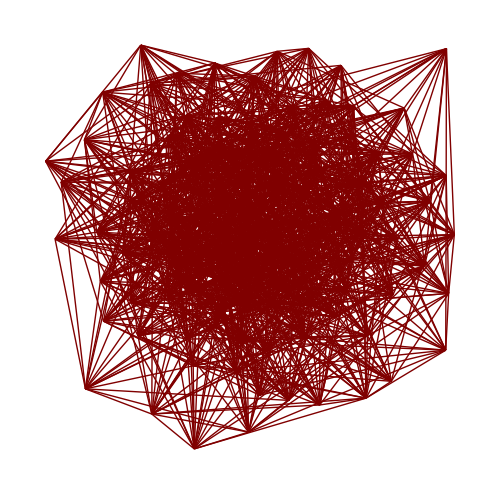

```mathematica
GraphPlot[Rule@@@(StringSplit[#,"."]&/@Keys[Flows[]]),ImageSize->500,VertexRenderingFunction->None]
```

```mathematica
BlockTimePlus[]
```

1

```mathematica
Timing[Harvest[#]&/@Keys[Flows[]];]
```

{0.07798,Null}

```mathematica
Table[Contos[ToString[c],"bala"],{c,100}]
```

{2393575482002880897049159162/41113491775332745943910645,21648000239746955542487741768729/597714885111885622539410092140,5650049173814842250172364699/152155888888856369382585720,590493574595718530619576641/21098637131784849733216120,1817475328446693074493166095191/54313399351586565388649571120,155991717884572896019838321483/6117775893187429160678869881,2584334702904509777781228959/87459147041328772289636238,102544755988695221911309/3940307790596605091664,704796719358231179815639519/31772589785858703624737895,15425785235820337234885673/790257482379499006228356,69656979729857060244536835/3132947746860733531746926,4608252849598173368/253898087162658939,868300011904141275167/38723655151158125148,479520365589919405672075/25625344579309650294504,122841393944812244276029139/6832792013598231715844964,4907377836823759511862620347/214782712380340184260652472,16571475083879112602094081380861/782968414712820566130887850864,774542365466834198581/58492246658279516082,728065064970030647003/39039740292322001232,9650291137745006105473/563126384138415401304,4452604998076872650583457/232296515682522576729444,28928103753080481140183/1664872489805403482604,9068308022952572690502781/599838638209332491429460,6689059251678146891/536539354004109456,97225857002811286549666764013/5870584942452284332922179536,41740716142113376703059/3336478695006056511912,665362111845587836278306479/41132776216556591992689264,1358700704776057413791/128009171242574748126,329278256741142009779/43607361030280929882,17137854014694978275/1468622585362729104,4445166763422181549/417827697599576880,453523121461462797739/48499328083175417448,2278966204467470400084155/140265835183610780635992,256520999055050021269/13706002693740122766,2612808300528022433351/248750427905282677374,4353735799865435/408677134231548,1304033699003513898339/93906750594229869296,678087845372610675/67913925071141968,380169256919593901/47280198147087906,1635680661361883/265212348884490,254467777506278627251589/22281460461216381300876,58250289533287851343/5361880290778806795,359483156980229/35577130217706,20740219723119601/1875384936137097,483817065/99085112,1098302303411/197852883844,103554221616800336707/9649342373830662888,73669446978982512563/8476224972542858916,90823115200871/13214971495089,10053347612021306423/1223238368994693480,33315576958156228279/3233129331397453488,15830075250851/2041814546408,785970236088431/76004537421072,6558830593/1598034357,388090018133/66457666296,79627101/19558448,730889944/253712909,6180664488065/821533409424,83406045033817/12077930184684,493249595/160831044,553875002779/129883653198,7997337199/1467827634,902000915/258030864,8538336679/1502698974,967493782565/279458391366,33633/11186,16277035/5163914,421397376797/68395619754,755/594,2612145/950011,84393/47242,8269425/3129448,20084923/6699693,6725265/3285584,299242679695/78535314352,81858375/22935359,120/97,897681695/288006192,149097/91471,10942984973/2228233560,2735/2993,6607070/1987821,1656655/895781,1978487/789360,0,40/97,1,68990/31349,553/391,7/10,100/79,629827/264422,0,0,0,0,2335/1363,0,45/47,0}

```mathematica
Total@Table[Contos[ToString[c],"bala"],{c,100}]
```

1000

#### Hint simulates mixed strategy of users choosing flows to settle

```mathematica
(* spec in progress *) 
?Hint
(* implementation in progress *)
```

Hint[d] suggests settlement for destination conto d.

```mathematica
Table[With[{is=Contos[ToString[k],"ifis"],os=Contos[ToString[k],"ofis"],h=Hint[ToString[k]]},If[EvenQ[k],h,If[Length[is]>0,RandomChoice[is],If[Length[os]>0,RandomChoice[os],0]]]],{k,Range[100]}]
```

{49.1,72.2,8.3,23.4,64.5,48.6,61.7,17.8,16.9,90.10,52.11,54.12,62.13,73.14,28.15,70.16,25.17,35.18,84.19,92.20,82.21,54.22,63.23,37.24,26.25,50.26,42.27,50.28,92.29,58.30,94.31,89.32,75.33,53.34,61.35,79.36,61.37,65.38,53.39,56.40,50.41,95.42,45.43,91.44,67.45,65.46,56.47,73.48,74.49,55.50,98.51,100.52,61.53,62.54,98.55,59.56,67.57,95.58,69.59,93.60,93.61,77.62,85.63,81.64,87.65,91.66,98.67,73.68,82.69,84.70,100.71,100.72,99.73,92.74,76.75,84.76,86.77,86.78,96.79,82.80,82.81,85.82,83.5,88.84,97.85,95.86,99.87,93.88,92.89,100.90,91.60,100.92,93.22,97.95,97.96,100.97,99.95}

#### Simulate all contos for 100 steps

```mathematica
Timing[cf100100=Table[(BlockTimePlus[];Table[Harvest[With[{is=Contos[ToString[k],"ifis"],os=Contos[ToString[k],"ofis"],h=Hint[ToString[k]]},If[EvenQ[k],h,If[Length[is]>0,RandomChoice[is],If[Length[os]>0,RandomChoice[os],0]]]]],{k,RandomSample[Range[100]]}];Contos[ToString[#],"bala"]&/@Range[100]),{s,100}];]
```

{26.802,Null}

#### Plots of 100 account balances for 100 steps.

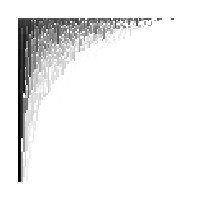
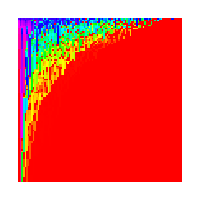
-Graphics--Graphics--Graphics-

```mathematica
Row[{ArrayPlot[N[cf100100]^.1,ImageSize->200],ArrayPlot[N[cf100100]^.1,ImageSize->200,ColorFunction->Hue],ArrayPlot[N[cf100100]^.1,ImageSize->200,ColorFunction->GrayLevel]}]
```

```mathematica
Total[Contos[ToString[#],"bala"]&/@Range[100]]
```

1000

#### Total of balances for all periods

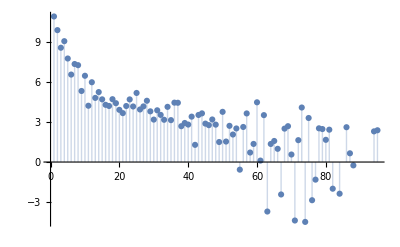

```mathematica
ListPlot[Log[Total@cf100100],Filling->Axis]
```

#### Total of balances for all periods and all odd versus even contos

```mathematica
Total/@Transpose@Partition[Total@cf100100,2]
```

{6456063536842807839032428881466022256334824064124449279948748885827920586867985581388199559650484636964538430059202307690449237753603000786158566843/96715543013531329472827545833001027747849210409901728226933060056951981461095031184107823751076451666363896832019635295276236800000000000000000,3215490764510325108250325701834080518450096976865723542744557119867277559241517537022582815457160529671851253142761221837174442246396999213841433157/96715543013531329472827545833001027747849210409901728226933060056951981461095031184107823751076451666363896832019635295276236800000000000000000}

```mathematica
N[Total/@Transpose@Partition[Total@cf100100,2]]
```

{66753.1,33246.9}

#### Even contos follow hints and get most of the pie.

```mathematica
PieChart[Total/@Transpose@Partition[Total@cf100100,2]]
```

-Graphics-

```mathematica
Total[Total/@Transpose@Partition[Total@cf100100,2]]/100
```

1000

```mathematica
Row[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]Dataset[<>]

## Export

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
Export["contoflowexport.json",<|"contoflows"-><|"contos"->Contos[],"flows"->Flows[]|>|>,"JSON"]
```

contoflowexport.json

## 10k contos

```mathematica
ContoFlowReset[]
```

```mathematica
Timing[Table[NewConto[ToString[n],Mod[n,2],10],{n,10000}];]
```

{0.110232,Null}

```mathematica
Timing[Table[Table[With[{rc=RandomInteger[{1,n}]},If[rc==n,Nothing,NewFlow[ToString[n],ToString[rc],RandomInteger[{1,10}]]]];,{m,20}],{n,1,10000}];]
```

{8.05389,Null}

#### Simulate 10k contos for 100 steps assuming 100 harvests per step

```mathematica
Timing[cf1000100=Table[(BlockTimePlus[];Table[Harvest[With[{is=Contos[ToString[k],"ifis"],os=Contos[ToString[k],"ofis"],h=Hint[ToString[k]]},If[EvenQ[k],h,If[Length[is]>0,RandomChoice[is],If[Length[os]>0,RandomChoice[os],0]]]]],{k,RandomSample[Range[10000],100]}];Contos[ToString[#],"bala"]&/@Range[10000]),{s,100}];]
```

{46.6351,Null}

#### Plots of 10k account balances in 100*100 array for 10 steps.

```mathematica
GraphicsGrid[Partition[ArrayPlot[Partition[#,100]]&/@cf1000100,10]]
```

-Graphics-

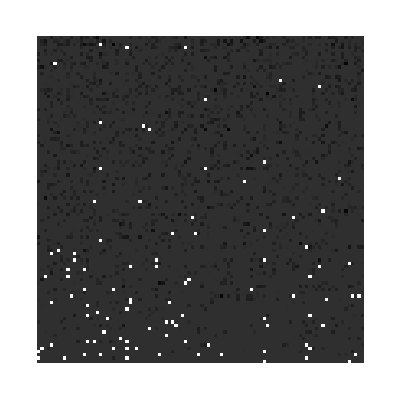

```mathematica
ArrayPlot[Partition[cf1000100[[1]],100]]
```

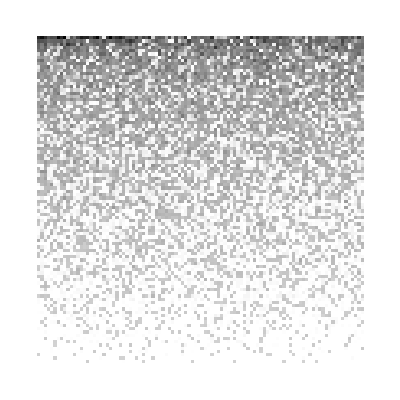

```mathematica
ArrayPlot[Partition[cf1000100[[100]],100]]
```

```mathematica
Total[Contos[ToString[#],"bala"]&/@Range[10000]]
```

100000

Larger numbers of participants requesting harvests sporadically may reduce the effect of following hints as generated with heuristics implemented in this version.

```mathematica
PieChart[Total/@Transpose@Partition[Total@cf1000100,2]]
```

-Graphics-